```mathematica
Wp[x_]:=Integrate[(1-2ξ Cos[ϕ]+ξ^2)^(1-α)Sin[ϕ],{ϕ,0,π}]
```

```mathematica
Wp[x]
```

$Aborted

```mathematica
Integrate[Sin[x](a^2-Cos[x])^b,{x,0,π}]
```

ConditionalExpression[(-(-1+a^2)^(1+b)+(1+a^2)^(1+b))/(1+b),(Re[ArcCos[a^2]]>π||Re[ArcCos[a^2]]<0||ArcSin[a^2]∉Reals)&&(Re[a^2]<-1||Re[a^2]>1||a^2∉Reals)]

```mathematica
(-(-1+a^2)^(1+b)+(1+a^2)^(1+b))/(1+b)/.a^2->1+ξ^2/.b->1-α
```

(-(ξ^2)^(2-α)+(2+ξ^2)^(2-α))/(2-α)

```mathematica
Assuming[1<α<2,Integrate[1/(√(-(A^2)^(2-α)+(2+A^2)^(2-α)-(-(ξ^2)^(2-α)+(2+ξ^2)^(2-α)))),{ξ,0,A}]]
```

∫_0^A 1/(√(-(A^2)^(2-α)+(2+A^2)^(2-α)+(ξ^2)^(2-α)-(2+ξ^2)^(2-α)))ⅆξ

```mathematica
Hold[NIntegrate[ⅈ/(√(-(A^2)^(2-α)+(2+A^2)^(2-α)-(-(ξ^2)^(2-α)+(2+ξ^2)^(2-α)))),{ξ,0,A}]]/.A->0.00001/.α->1.5//ReleaseHold
```

0.00632455+0. ⅈ

```mathematica
DensityPlot[Re[Hold[NIntegrate[1/(√((A^2)^(2-α)-(2+A^2)^(2-α)+(-(ξ^2)^(2-α)+(2+ξ^2)^(2-α)))),{ξ,0,A}]]//ReleaseHold],{A,0,1},{α,1,2},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotPoints->50]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {0.000020359633843259800063544923620032639499655147119483444839715957642}. NIntegrate obtained 71.6845-0.0691062 ⅈ and 0.185071 for the integral and error estimates.

NIntegrate::inumri: The integrand 1/(√(-2.-(ξ^2)^1.+(2+ξ^2)^1.)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.00255102}}.

NIntegrate::inumri: The integrand 1/(√(-2.-(ξ^2)^1.+(2+ξ^2)^1.)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.00127551}}.

NIntegrate::inumri: The integrand 1/(√(-2.-(ξ^2)^1.+(2+ξ^2)^1.)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.000637755}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {0.000214241}. NIntegrate obtained 7592.16 and 870.69 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {0.000029111}. NIntegrate obtained 7605. and 797.161 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{0.0204082,0.02040816326530607691131688390479108901904066214954568314294693185}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

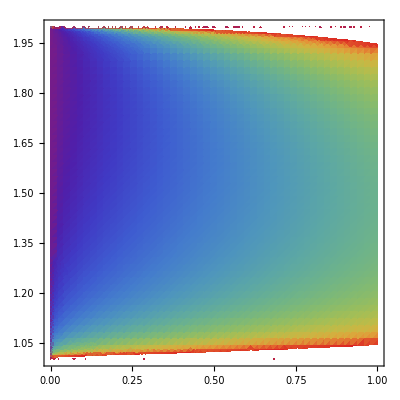
```mathematica
Export["period.jpg",-Graphics-]
```

period.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["period.jpg"]]]
```

```mathematica
SystemOpen["period.pdf"]
```

```mathematica
SystemOpen["period.pdf"]
```